```mathematica
Integrate[1/(1-ω+ⅈ δ)*1/(ω^2-c^2+ⅈ δ),{ω,-∞,∞},PrincipalValue->True,Assumptions->{δ>0,c>0}]
```

$Aborted

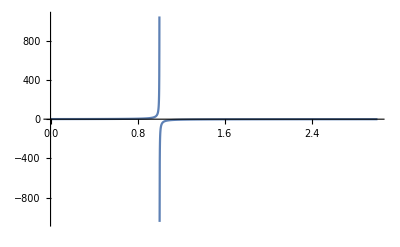

```mathematica
Plot[1/(1-x),{x,0,3},PlotRange->All]
```

```mathematica
Integrate[1/(ϵ-ξ-ω+ⅈ δ*Sign[ξ])*c/(ω-c+ⅈ δ)*c/(ω+c-ⅈ δ),{ω,-∞,∞},Assumptions->{ϵ∈Reals,c>0,δ>0,ξ>0}]
Integrate[1/(ϵ-ξ-ω+ⅈ δ*Sign[ξ])*c/(ω-c+ⅈ δ)*c/(ω+c-ⅈ δ),{ω,-∞,∞},Assumptions->{ϵ∈Reals,c>0,δ>0,ξ<0}]
```

(ⅈ c^2 π)/((c-ⅈ δ) (c-2 ⅈ δ-ϵ+ξ))

-(ⅈ c^2 π)/((c-ⅈ δ) (c-2 ⅈ δ+ϵ-ξ))

```mathematica
Expand[(c-ⅈ δ) (ϵ-c-ξ+2ⅈ δ)]~Collect~δ
Expand[(c-ⅈ δ) (c-2 ⅈ δ+ϵ-ξ)]~Collect~δ
```

-c^2+2 δ^2+c ϵ+δ (3 ⅈ c-ⅈ ϵ+ⅈ ξ)-c ξ

c^2-2 δ^2+c ϵ+δ (-3 ⅈ c-ⅈ ϵ+ⅈ ξ)-c ξ

```mathematica
f[ω_]:=1/(ϵ-ξ-ω+ⅈ δ*Sign[ξ])*c/(ω-c+ⅈ δ)*c/(ω+c-ⅈ δ);
Residue[f[ω],{ω,ϵ-ξ+ⅈ δ*Sign[ξ]}]//Simplify
```

c^2/((c-ⅈ δ-ϵ+ξ-ⅈ δ Sign[ξ]) (c-ⅈ δ+ϵ-ξ+ⅈ δ Sign[ξ]))

```mathematica
Limit[Integrate[Log[(α-x-β)/(α-x)]*(x^4 δ)/(x^2-δ^2),x,Assumptions->{β>0,α>0}],δ->0]
```

0

```mathematica
Integrate[δ/((1+x)x^2(1+δ^2)),{x,-ϵ,ϵ},Assumptions->{ϵ>5,δ>0},PrincipalValue->True]
```

Integrate[δ/(x^2 (1+x) (1+δ^2)),{x,-ϵ,ϵ},Assumptions→{ϵ>5,δ>0},PrincipalValue→True]

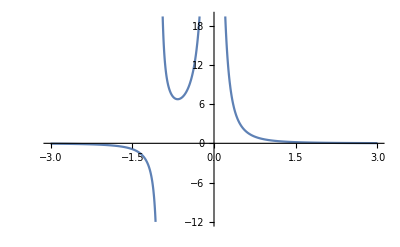

```mathematica
Plot[1/(x^2(1+x)),{x,-3,3}]
```

```mathematica
Integrate[δ/((α+v x)(c^2-δ^2)),{x,-α/v+ϵ,∞},Assumptions->{c>0,α>0,p>0,q>0,ϵ>0,δ>0}]
```

Integrate[δ/((v x+α) (1+δ^2)),{x,-α/v+ϵ,∞},Assumptions→{α>0,p>0,q>0,ϵ>0,δ>0}]

```mathematica
Limit[(π+2 ArcCot[(α δ)/(α^2+p q (p q-α ϵ))])/(2 p q)+ArcTan[(α δ)/(α^2+p q (p q+α ϵ))]/(p q),ϵ->0]
```

$Aborted

```mathematica
f[x_]:=(x^4*δ)/((x^2-δ^2)(α-x-p1));
Integrate[f[x],{x,0,α},Assumptions->{α>0,δ>0,p1∈Reals}]
```

ConditionalExpression[-((δ (-2 p1^3 α+7 p1^2 α^2-8 p1 α^3+3 α^4+2 p1 α δ^2-3 α^2 δ^2+2 (p1-α)^4 Log[p1]-2 (p1-α)^4 Log[p1-α]+2 δ^4 Log[δ]+p1 δ^3 Log[-α+δ]-α δ^3 Log[-α+δ]-p1 δ^3 Log[α+δ]+α δ^3 Log[α+δ]-δ^4 Log[-α^2+δ^2]))/(2 (p1^2-2 p1 α+α^2-δ^2))),α≤δ&&p1≥α]

```mathematica
Integrate[-((δ (-2 p1^3 α+7 p1^2 α^2-8 p1 α^3+3 α^4+2 p1 α δ^2-3 α^2 δ^2+2 (p1-α)^4 Log[p1]-2 (p1-α)^4 Log[p1-α]+2 δ^4 Log[δ]+p1 δ^3 Log[-α+δ]-α δ^3 Log[-α+δ]-p1 δ^3 Log[α+δ]+α δ^3 Log[α+δ]-δ^4 Log[-α^2+δ^2]))/(2 (p1^2-2 p1 α+α^2-δ^2))),{p1,-α,α},Assumptions->{α>δ>0,p1∈Reals}]
```

Integrate[-((δ (-2 p1^3 α+7 p1^2 α^2-8 p1 α^3+3 α^4+2 p1 α δ^2-3 α^2 δ^2+2 (p1-α)^4 Log[p1]-2 (p1-α)^4 Log[p1-α]+2 δ^4 Log[δ]+p1 δ^3 Log[-α+δ]-α δ^3 Log[-α+δ]-p1 δ^3 Log[α+δ]+α δ^3 Log[α+δ]-δ^4 Log[-α^2+δ^2]))/(2 (p1^2-2 p1 α+α^2-δ^2))),{p1,-α,α},Assumptions→{α>δ>0,p1∈Reals}]

```mathematica
Limit[%,δ->0]
```

```mathematica
ConditionalExpression[0,α≤0]
```